# Superimposed Kerr Metric in Kerr-Schild coordinates.

## Analytic

### Trajectory

In order to choose a trajectory, we need to choose a spatial velocity in the form
v_(a)=β_(a)(n⃗)_a(t)

```mathematica
ClearAll[Ω];
Ω=√((M1+M2)/b^3);
ClearAll[β,nx,ny];
β[bhIdx_]=(b*Ω)/2;

nx[bhIdx_,t_]=(-1)^bhIdx Sin[Ω*t];
ny[bhIdx_,t_]=(-1)^(bhIdx+1)Cos[Ω*t];

ClearAll[v,sx,sy,γ];
v[bhIdx_,t_]=FullSimplify[β[bhIdx]*{nx[bhIdx,t],ny[bhIdx,t],0}];
sx[bhIdx_,t_]=FullSimplify[Integrate[v[bhIdx,tp]⟦1⟧,tp]//.tp->t];
sy[bhIdx_,t_]=FullSimplify[Integrate[v[bhIdx,tp]⟦2⟧,tp]//.tp->t];
γ[bhIdx_,t_]=FullSimplify[1/Sqrt[1-v[bhIdx,t].v[bhIdx,t]]];
```

### Local Coordinates

```mathematica
ClearAll[eqt,eqx,eqy,eqz];
eqt[bhIdx_,T_,X_,Y_,Z_,t_]:=γ[bhIdx,t](T-β[bhIdx](nx[bhIdx,t]*X+ny[bhIdx,t]*Y));
eqx[bhIdx_,T_,X_,Y_,Z_,t_]:=sx[bhIdx,t]+X(1+(γ[bhIdx,t]-1)nx[bhIdx,t]^2)+Y(-(γ[bhIdx,t]-1)nx[bhIdx,t]ny[bhIdx,t]);
eqy[bhIdx_,T_,X_,Y_,Z_,t_]:=sy[bhIdx,t]+X(-(γ[bhIdx,t]-1)nx[bhIdx,t]ny[bhIdx,t])+Y(1+(γ[bhIdx,t]-1)ny[bhIdx,t]^2);
eqz[bhIdx_,T_,X_,Y_,Z_,t_]:=Z;

ClearAll[global2localsol];
global2localsol=FullSimplify[
Solve[
{
eqt[bhIdx,T,X,Y,Z,t]==t,
eqx[bhIdx,T,X,Y,Z,t]==x,
eqy[bhIdx,T,X,Y,Z,t]==y,
eqz[bhIdx,T,X,Y,Z,t]==z
},
{T,X,Y,Z}
],
bhIdx∈Integers
]//Flatten;

ClearAll[eqt,eqx,eqy,eqz];

FullSimplify[T//.global2localsol]
FullSimplify[X//.global2localsol]
FullSimplify[Y//.global2localsol]
FullSimplify[Z//.global2localsol]
```

1/16 (8 √(-(-4 b+M1+M2)/b) t-2 (-1)^bhIdx b √((M1+M2)/b^3) (-2+√(-(-4 b+M1+M2)/b)) y Cos[(3 √(M1+M2) t)/b^(3/2)]-2 (-1)^bhIdx b √((M1+M2)/b^3) (2+√(-(-4 b+M1+M2)/b)) y Cos[√((M1+M2)/b^3) t]+(√(M1+M2) (2 (-1)^bhIdx (2+√(-(-4 b+M1+M2)/b)) x Sin[(√(M1+M2) t)/b^(3/2)]-(-2+√(-(-4 b+M1+M2)/b)) (2 (-1)^bhIdx x Sin[(3 √(M1+M2) t)/b^(3/2)]+b Sin[(4 √(M1+M2) t)/b^(3/2)])))/(√b))

1/8 (2 (2+√(-(-4 b+M1+M2)/b)) x+(-1)^bhIdx b (2+√(-(-4 b+M1+M2)/b)) Cos[√((M1+M2)/b^3) t]+4 x Cos[2 √((M1+M2)/b^3) t]+2 (-1)^bhIdx b Cos[3 √((M1+M2)/b^3) t]-4 y Sin[2 √((M1+M2)/b^3) t]-√(-(-4 b+M1+M2)/b) (2 x Cos[2 √((M1+M2)/b^3) t]+(-1)^bhIdx b Cos[3 √((M1+M2)/b^3) t]-2 y Sin[2 √((M1+M2)/b^3) t]))

-(2 (M1+M2) y+2 (M1+M2+4 b (-2+√(-(-4 b+M1+M2)/b))) y Cos[2 √((M1+M2)/b^3) t]+(-1)^bhIdx b (M1+M2) Sin[√((M1+M2)/b^3) t]+(M1+M2+4 b (-2+√(-(-4 b+M1+M2)/b))) (2 x Sin[2 √((M1+M2)/b^3) t]+(-1)^bhIdx b Sin[3 √((M1+M2)/b^3) t]))/(8 b (-2+√(-(-4 b+M1+M2)/b)))

z

```mathematica
ClearAll[eqT,eqX,eqY,eqZ];
eqT[bhIdx_,M1_,M2_,b_,t_,x_,y_,z_]:=1/16 (8 √(-(-4 b+M1+M2)/b) t-2 (-1)^bhIdx b √((M1+M2)/b^3) (-2+√(-(-4 b+M1+M2)/b)) y Cos[(3 √(M1+M2) t)/b^(3/2)]-2 (-1)^bhIdx b √((M1+M2)/b^3) (2+√(-(-4 b+M1+M2)/b)) y Cos[√((M1+M2)/b^3) t]+(√(M1+M2) (2 (-1)^bhIdx (2+√(-(-4 b+M1+M2)/b)) x Sin[(√(M1+M2) t)/b^(3/2)]-(-2+√(-(-4 b+M1+M2)/b)) (2 (-1)^bhIdx x Sin[(3 √(M1+M2) t)/b^(3/2)]+b Sin[(4 √(M1+M2) t)/b^(3/2)])))/(√b));

eqX[bhIdx_,M1_,M2_,b_,t_,x_,y_,z_]:=1/8 (2 (2+√(-(-4 b+M1+M2)/b)) x+(-1)^bhIdx b (2+√(-(-4 b+M1+M2)/b)) Cos[√((M1+M2)/b^3) t]+4 x Cos[2 √((M1+M2)/b^3) t]+2 (-1)^bhIdx b Cos[3 √((M1+M2)/b^3) t]-4 y Sin[2 √((M1+M2)/b^3) t]-√(-(-4 b+M1+M2)/b) (2 x Cos[2 √((M1+M2)/b^3) t]+(-1)^bhIdx b Cos[3 √((M1+M2)/b^3) t]-2 y Sin[2 √((M1+M2)/b^3) t]));

eqY[bhIdx_,M1_,M2_,b_,t_,x_,y_,z_]:=-(2 (M1+M2) y+2 (M1+M2+4 b (-2+√(-(-4 b+M1+M2)/b))) y Cos[2 √((M1+M2)/b^3) t]+(-1)^bhIdx b (M1+M2) Sin[√((M1+M2)/b^3) t]+(M1+M2+4 b (-2+√(-(-4 b+M1+M2)/b))) (2 x Sin[2 √((M1+M2)/b^3) t]+(-1)^bhIdx b Sin[3 √((M1+M2)/b^3) t]))/(8 b (-2+√(-(-4 b+M1+M2)/b)));

eqZ[bhIdx_,M1_,M2_,b_,t_,x_,y_,z_]:=z;
```

### Single KS metric aux functions

```mathematica
ClearAll[r,H,l1,l2,l3];
r[a_,X_,Y_,Z_]:=√(1/2(-a^2+X^2+Y^2+Z^2+√(4 a^2 Z^2+(-a^2+X^2+Y^2+Z^2)^2)));
H[M_,a_,X_,Y_,Z_]:=(M*r[a,X,Y,Z])/(r[a,X,Y,Z]^2+a^2*(Z/r[a,X,Y,Z])^2);
l1[a_,X_,Y_,Z_]:=(r[a,X,Y,Z]*X+a*Y)/(r[a,X,Y,Z]^2+a^2);
l2[a_,X_,Y_,Z_]:=(r[a,X,Y,Z]*Y-a*X)/(r[a,X,Y,Z]^2+a^2);
l3[a_,X_,Y_,Z_]:=Z/r[a,X,Y,Z];


ClearAll[ℋ];
ℋ[M_,a_,X_,Y_,Z_]:=
ParallelTable[
2*H[M,a,X,Y,Z]*{1,l1[a,X,Y,Z],l2[a,X,Y,Z],l3[a,X,Y,Z]}⟦μ⟧{1,l1[a,X,Y,Z],l2[a,X,Y,Z],l3[a,X,Y,Z]}⟦ν⟧
,{μ,1,4},{ν,1,4}
];
```

### Jacobians

```mathematica
ClearAll[J];
J[bhIdx_,M1_,M2_,b_,t_,x_,y_,z_]:=ParallelTable[
FullSimplify[
D[
{eqT[bhIdx,M1,M2,b,t,x,y,z],eqX[bhIdx,M1,M2,b,t,x,y,z],eqY[bhIdx,M1,M2,b,t,x,y,z],eqZ[bhIdx,M1,M2,b,t,x,y,z]}⟦i⟧,
{t,x,y,z}⟦j⟧
]
],
{i,1,4},
{j,1,4}
]
```

### 4-metric assembly

```mathematica
ClearAll[llgSKS];
llgSKS=Module[
{η,Ω,T1,X1,Y1,Z1,T2,X2,Y2,Z2,r1,r2,ℋ1,ℋ2,J1,J2,bh1,bh2},

Print["Computing η"];
η=DiagonalMatrix[{-1,1,1,1}];

Print["Computing T1,...,Z1"];
T1=eqT[0,M1,M2,b,t,x,y,z];
X1=eqT[0,M1,M2,b,t,x,y,z];
Y1=eqT[0,M1,M2,b,t,x,y,z];
Z1=eqT[0,M1,M2,b,t,x,y,z];

Print["Computing T2,...,Z2"];
T2=eqT[1,M1,M2,b,t,x,y,z];
X2=eqT[1,M1,M2,b,t,x,y,z];
Y2=eqT[1,M1,M2,b,t,x,y,z];
Z2=eqT[1,M1,M2,b,t,x,y,z];

Print["Computing r1,r2"];
r1=r[a1,X1,Y1,Z1];
r2=r[a2,X2,Y2,Z2];

Print["Computing ℋ1,ℋ2"];
ℋ1=ℋ[M1,a1,X1,Y1,Z1];
ℋ2=ℋ[M2,a2,X2,Y2,Z2];

Print["Computing J1,J2"];
J1=J[0,M1,M2,b,t,x,y,z];
J2=J[1,M1,M2,b,t,x,y,z];

Print["Contracting"];
bh1=Table[Sum[J1⟦ab,μ⟧J1⟦bb,ν⟧ℋ1⟦ab,bb⟧,{ab,1,4},{bb,1,4}],{μ,1,4},{ν,1,4}];
bh2=Table[Sum[J2⟦ab,μ⟧J2⟦bb,ν⟧ℋ2⟦ab,bb⟧,{ab,1,4},{bb,1,4}],{μ,1,4},{ν,1,4}];

Return[(η+bh1+bh2)]
];
```

Computing η

Computing T1,...,Z1

Computing T2,...,Z2

Computing r1,r2

Computing ℋ1,ℋ2

$Aborted

```mathematica
ClearAll[uugSKS];
uugSKS=Compile[{{M1,_Real},{a1,_Real},{M2,_Real},{a2,_Real},{b,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},
Inverse[llgSKS[M1,M2,a1,a2,b,t,x,y,z]]
];
```

## Compiled

### Trajectory

In order to choose a trajectory, we need to choose a spatial velocity in the form
v_(a)=β_(a)(n⃗)_a(t)

```mathematica
ClearAll[β,nx,ny];
β[bhIdx_]=(b*Ω)/2;

nx[bhIdx_,t_]=(-1)^bhIdx Sin[Ω*t];
ny[bhIdx_,t_]=(-1)^(bhIdx+1)Cos[Ω*t];

ClearAll[v,sx,sy,γ];
v[bhIdx_,t_]=FullSimplify[β[bhIdx]*{nx[bhIdx,t],ny[bhIdx,t],0}];
sx[bhIdx_,t_]=FullSimplify[Integrate[v[bhIdx,tp]⟦1⟧,tp]//.tp->t];
sy[bhIdx_,t_]=FullSimplify[Integrate[v[bhIdx,tp]⟦2⟧,tp]//.tp->t];
γ[bhIdx_,t_]=FullSimplify[1/Sqrt[1-v[bhIdx,t].v[bhIdx,t]]];
```

### Local Coordinates

```mathematica
ClearAll[eqt,eqx,eqy,eqz];
eqt[bhIdx_,T_,X_,Y_,Z_,t_]:=γ[bhIdx,t](T-β[bhIdx](nx[bhIdx,t]*X+ny[bhIdx,t]*Y));
eqx[bhIdx_,T_,X_,Y_,Z_,t_]:=sx[bhIdx,t]+X(1+(γ[bhIdx,t]-1)nx[bhIdx,t]^2)+Y(-(γ[bhIdx,t]-1)nx[bhIdx,t]ny[bhIdx,t]);
eqy[bhIdx_,T_,X_,Y_,Z_,t_]:=sy[bhIdx,t]+X(-(γ[bhIdx,t]-1)nx[bhIdx,t]ny[bhIdx,t])+Y(1+(γ[bhIdx,t]-1)ny[bhIdx,t]^2);
eqz[bhIdx_,T_,X_,Y_,Z_,t_]:=Z;

ClearAll[global2localsol];
global2localsol=FullSimplify[
Solve[
{
eqt[bhIdx,T,X,Y,Z,t]==t,
eqx[bhIdx,T,X,Y,Z,t]==x,
eqy[bhIdx,T,X,Y,Z,t]==y,
eqz[bhIdx,T,X,Y,Z,t]==z
},
{T,X,Y,Z}
],
bhIdx∈Integers
]//Flatten;

ClearAll[eqt,eqx,eqy,eqz];

ClearAll[eqT,eqX,eqY,eqZ];
eqT=Compile[{{bhIdx,_Integer},{b,_Real},{Ω,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},Evaluate[T//.global2localsol]];
eqX=Compile[{{bhIdx,_Integer},{b,_Real},{Ω,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},Evaluate[X//.global2localsol]];
eqY=Compile[{{bhIdx,_Integer},{b,_Real},{Ω,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},Evaluate[Y//.global2localsol]];
eqZ=Compile[{{bhIdx,_Integer},{b,_Real},{Ω,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},Evaluate[Z//.global2localsol]];
```

### Single KS metric aux functions

```mathematica
ClearAll[r,H,l1,l2,l3];
r=Compile[{{a,_Real},{X,_Real},{Y,_Real},{Z,_Real}},√(1/2(-a^2+X^2+Y^2+Z^2+√(4 a^2 Z^2+(-a^2+X^2+Y^2+Z^2)^2)))];
H=Compile[{{M,_Real},{a,_Real},{X,_Real},{Y,_Real},{Z,_Real}},(M*r[a,X,Y,Z])/(r[a,X,Y,Z]^2+a^2*(Z/r[a,X,Y,Z])^2)];
l1=Compile[{{a,_Real},{X,_Real},{Y,_Real},{Z,_Real}},(r[a,X,Y,Z]*X+a*Y)/(r[a,X,Y,Z]^2+a^2)];
l2=Compile[{{a,_Real},{X,_Real},{Y,_Real},{Z,_Real}},(r[a,X,Y,Z]*Y-a*X)/(r[a,X,Y,Z]^2+a^2)];
l3=Compile[{{a,_Real},{X,_Real},{Y,_Real},{Z,_Real}},Z/r[a,X,Y,Z]];


ClearAll[ℋ];
ℋ=Compile[{{M,_Real},{a,_Real},{X,_Real},{Y,_Real},{Z,_Real}},
Table[
2*H[M,a,X,Y,Z]*{1,l1[a,X,Y,Z],l2[a,X,Y,Z],l3[a,X,Y,Z]}⟦μ⟧{1,l1[a,X,Y,Z],l2[a,X,Y,Z],l3[a,X,Y,Z]}⟦ν⟧,{μ,1,4},{ν,1,4}
]
];
```

### Finite difference derivative

```mathematica
ClearAll[fd18];
fd18[f_,vars_,idx_,h_]:=Module[
{m4,m3,m2,m1,p1,p2,p3,p4,num,den},
m4=vars+Table[If[i==idx,-4h,0],{i,1,Length[vars]}];
m3=vars+Table[If[i==idx,-3h,0],{i,1,Length[vars]}];
m2=vars+Table[If[i==idx,-2h,0],{i,1,Length[vars]}];
m1=vars+Table[If[i==idx,-1h,0],{i,1,Length[vars]}];
p1=vars+Table[If[i==idx,+1h,0],{i,1,Length[vars]}];
p2=vars+Table[If[i==idx,+2h,0],{i,1,Length[vars]}];
p3=vars+Table[If[i==idx,+3h,0],{i,1,Length[vars]}];
p4=vars+Table[If[i==idx,+4h,0],{i,1,Length[vars]}];

num=3*Apply[f,m4]-32*Apply[f,m3]+168*Apply[f,m2]-672*Apply[f,m1]+672*Apply[f,p1]-168*Apply[f,p2]+32*Apply[f,p3]-3*Apply[f,p4];
den=1/(840*h);

Return[num*den];
];
```

### Jacobians

```mathematica
ClearAll[J];
J=Compile[{{bhIdx,_Integer},{b,_Real},{Ω,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},
Table[fd18[{eqT,eqX,eqY,eqZ}⟦i⟧,{bhIdx,b,Ω,t,x,y,z},{4,5,6,7}⟦j⟧,1],{i,1,4},{j,1,4}]
];
```

### 4-metric assembly

```mathematica
ClearAll[llgSKS];
llgSKS=Compile[{{M1,_Real},{a1,_Real},{M2,_Real},{a2,_Real},{b,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},
Module[
{η,Ω,T1,X1,Y1,Z1,T2,X2,Y2,Z2,r1,r2,ℋ1,ℋ2,J1,J2,bh1,bh2},

η=DiagonalMatrix[{-1,1,1,1}];

Ω=Sqrt[(M1+M2)/b^3];

T1=eqT[0,b,Ω,t,x,y,z];
X1=eqX[0,b,Ω,t,x,y,z];
Y1=eqY[0,b,Ω,t,x,y,z];
Z1=eqZ[0,b,Ω,t,x,y,z];

T2=eqT[1,b,Ω,t,x,y,z];
X2=eqX[1,b,Ω,t,x,y,z];
Y2=eqY[1,b,Ω,t,x,y,z];
Z2=eqZ[1,b,Ω,t,x,y,z];

r1=r[a1,X1,Y1,Z1];
r2=r[a2,X2,Y2,Z2];

ℋ1=ℋ[M1,a1,X1,Y1,Z1];
ℋ2=ℋ[M2,a2,X2,Y2,Z2];

J1=J[0,b,Ω,t,x,y,z];
J2=J[1,b,Ω,t,x,y,z];

bh1=Table[Sum[J1⟦ab,μ⟧J1⟦bb,ν⟧ℋ1⟦ab,bb⟧,{ab,1,4},{bb,1,4}],{μ,1,4},{ν,1,4}];
bh2=Table[Sum[J2⟦ab,μ⟧J2⟦bb,ν⟧ℋ2⟦ab,bb⟧,{ab,1,4},{bb,1,4}],{μ,1,4},{ν,1,4}];

Return[(η+bh1+bh2)]
]
];
```

```mathematica
ClearAll[uugSKS];
uugSKS=Compile[{{M1,_Real},{a1,_Real},{M2,_Real},{a2,_Real},{b,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},
Inverse[llgSKS[M1,M2,a1,a2,b,t,x,y,z]]
];
```

### Connection

```mathematica
ClearAll[Γ]
Γ=Compile[{{M1,_Real},{a1,_Real},{M2,_Real},{a2,_Real},{b,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},
Module[
{uug,dllg},
uug=uugSKS[M1,a1,M2,a2,b,t,x,y,z];
dllg={
fd18[llgSKS,{M1,M2,a1,a2,b,t,x,y,z},6,1],
fd18[llgSKS,{M1,M2,a1,a2,b,t,x,y,z},7,1],
fd18[llgSKS,{M1,M2,a1,a2,b,t,x,y,z},8,1],
fd18[llgSKS,{M1,M2,a1,a2,b,t,x,y,z},9,1]
};

ParallelTable[
1/2 Sum[
uug⟦κ,δ⟧((dllg⟦α⟧)⟦β,δ⟧+(dllg⟦β⟧)⟦α,δ⟧-(dllg⟦δ⟧)⟦α,β⟧),
{δ,1,4}
],
{κ,1,4},
{α,1,4},
{β,1,4}
]
],
{{uugSKS[_,_,_,_,_,_,_,_,_],_Real,2},{fd18[_,_,_,_],_Real,2},{ParallelTable[_,_,_,_],_Real,3}}(*Decler return type as rank 3 real tensor *)
];
```

### Ricci

```mathematica
ClearAll[R]
R=Compile[{{M1,_Real},{a1,_Real},{M2,_Real},{a2,_Real},{b,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},
Module[
{localΓ,dΓ,p1,p2,p3},
localΓ=Γ[M1,a1,M2,a2,b,t,x,y,z];
dΓ={
fd18[Γ,{M1,M2,a1,a2,b,t,x,y,z},6,1],
fd18[Γ,{M1,M2,a1,a2,b,t,x,y,z},7,1],
fd18[Γ,{M1,M2,a1,a2,b,t,x,y,z},8,1],
fd18[Γ,{M1,M2,a1,a2,b,t,x,y,z},9,1]
};

p1=ParallelTable[Sum[(dΓ⟦α⟧)⟦α,i,j⟧,{α,1,4}],{i,1,4},{j,1,4}];
p2=ParallelTable[Sum[(dΓ⟦j⟧)⟦α,α,i⟧,{α,1,4}],{i,1,4},{j,1,4}];
p3=ParallelTable[Sum[localΓ⟦α,α,β⟧localΓ⟦β,i,j⟧-localΓ⟦α,i,β⟧localΓ⟦β,α,j⟧,{α,1,4},{β,1,4}],{i,1,4},{j,1,4}];

Return[p1-p2+p3]
],
{{Γ[_,_,_,_,_,_,_,_,_],_Real,3},{fd18[_,_,_,_],_Real,3},{ParallelTable[_,_,_],_Real,2}}
];

ClearAll[trR];
trR=Compile[{{M1,_Real},{a1,_Real},{M2,_Real},{a2,_Real},{b,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},
Module[
{uug,localR},
uug=uugSKS[M1,a1,M2,a2,b,t,x,y,z];
localR=R[M1,a1,M2,a2,b,t,x,y,z];
Sum[uug⟦i,j⟧localR⟦i,j⟧,{i,1,4},{j,1,4}]
],
{{uugSKS[_,_,_,_,_,_,_,_,_],_Real,2},{R[_,_,_,_,_,_,_,_,_],_Real,2},{Sum[_,_,_],_Real}}
];
```

## Plots

### R

```mathematica
ClearAll[M1,M2,a1,a2,b,Ω,time];
M1=1/2;
M2=1/2;

a1=9/10*M1;
a2=9/10*M2;

b=4;
Ω=Sqrt[(M1+M2)/b^3];

time=0;

ClearAll[x0,xf,points];
x0=-4;
xf=4;
points=11;

ClearAll[ki,kf];
ki=0;
kf=1;

ClearAll[data];
data=Table[trR[M1,M2,a1,a2,b,time,xi,yi,1],{xi,x0,xf,(xf-x0)/points},{yi,x0,xf,(xf-x0)/points}];

(*DensityPlot[
R[M1,M2,a1,a2,b,time,x,y,0],

{x,x0,xf},
{y,x0,xf},

PlotRange->{Automatic,Automatic,{ki,kf}},
PlotLegends->BarLegend[{Automatic,{ki,kf}}],

ColorFunctionScaling->False,
ColorFunction->(ColorData["DarkRainbow"][Rescale[#,{ki,kf}]]&),

PlotPoints->50,

ImageSize->Large
]*)
ClearAll[ki,kf];

ClearAll[M1,M2,a1,a2,b,Ω,time];
ClearAll[lapse];
ClearAll[x0,xf,points];
```

CompiledFunction::cfne: Numerical error encountered; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfne will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

CompiledFunction::cfte: Compiled expression {{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}} should be a rank 2 tensor of machine-size real numbers.

CompiledFunction::cfex: Could not complete external evaluation at instruction 5; proceeding with uncompiled evaluation.

CompiledFunction::cfte: Compiled expression {{{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{«1»},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}},{{Indeterminate,«3»},«3»},{{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}}} should be a rank 3 tensor of machine-size real numbers.

CompiledFunction::cfex: Could not complete external evaluation at instruction 3; proceeding with uncompiled evaluation.

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction::cfex will be suppressed during this calculation.

CompiledFunction::cfte: Compiled expression {{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}} should be a rank 2 tensor of machine-size real numbers.

General::stop: Further output of CompiledFunction::cfte will be suppressed during this calculation.

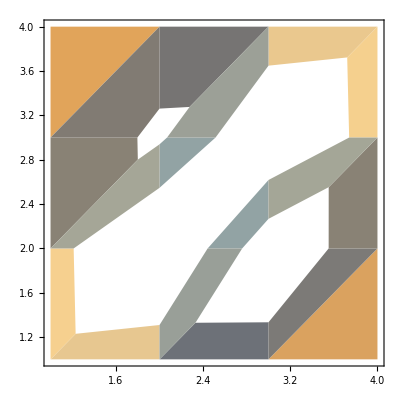

```mathematica
ListDensityPlot[{{0.006851621018253741,-0.03849680052731026,-0.036865917488866,0.0011425025926117649},{0.015988869225181186,0.40137306087759156,-0.28628980407911625,0.014475648848326273},{0.012602804604427559,-0.15408147310188158,0.33578855368351895,0.014212825416294187},{0.002435656869923832,-0.02438597502384437,-0.031452708455792296,0.006226160392039552}}]
```

### Lapse

CompiledFunction::cfsa: Argument x at position 7 should be a machine-size real number.

CompiledFunction::cfsa: Argument x at position 5 should be a machine-size real number.

General::stop: Further output of CompiledFunction::cfsa will be suppressed during this calculation.

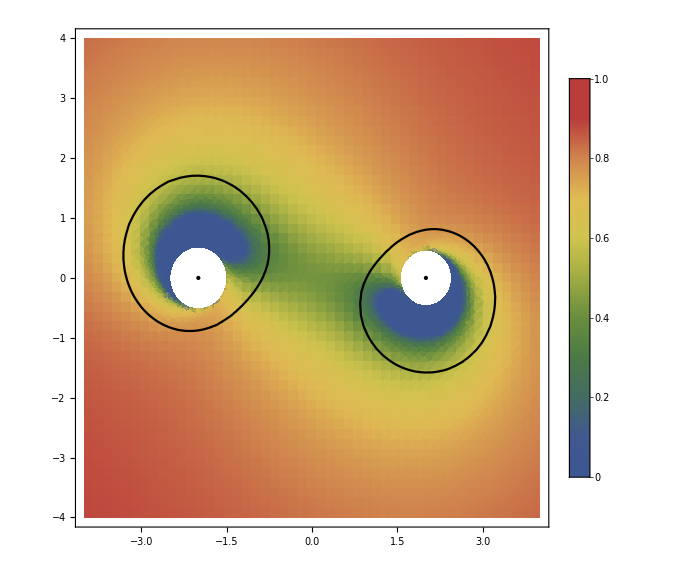

```mathematica
ClearAll[M1,M2,a1,a2,b,Ω,time];
M1=1/2;
M2=1/2;

a1=9/10*M1;
a2=9/10*M2;

b=4;
Ω=Sqrt[(M1+M2)/b^3];

time=0;

ClearAll[lapse];
lapse=Compile[{{M1,_Real},{a1,_Real},{M2,_Real},{a2,_Real},{b,_Real},{t,_Real},{x,_Real},{y,_Real},{z,_Real}},
Module[
{radicand},
radicand=-1/uugSKS[M1,M2,a1,a2,b,t,x,y,z]⟦1,1⟧;
If[radicand>0,Sqrt[radicand],0]
]
];

ClearAll[x0,xf];
x0=-4;
xf=4;

ClearAll[ki,kf];
ki=0;
kf=1;

Show[
DensityPlot[
lapse[M1,M2,a1,a2,b,time,x,y,0],

{x,x0,xf},
{y,x0,xf},

PlotRange->{Automatic,Automatic,{ki,kf}},
PlotLegends->BarLegend[{Automatic,{ki,kf}}],

ColorFunctionScaling->False,
ColorFunction->(ColorData["DarkRainbow"][Rescale[#,{ki,kf}]]&),

PlotPoints->50,

ImageSize->Large
],

ContourPlot[Evaluate[llgSKS[M1,M2,a1,a2,b,time,x,y,0]⟦1,1⟧]==0,{x,x0,xf},{y,x0,xf},ContourShading->None,ContourStyle->Directive[Black,Thick],PlotPoints->20],
Graphics[Point[{sx[0,time],sy[0,time]}]],
Graphics[Point[{sx[1,time],sy[1,time]}]]
]
ClearAll[ki,kf];

ClearAll[M1,M2,a1,a2,b,Ω,time];
ClearAll[lapse];
ClearAll[x0,xf];
```